```mathematica
k:= Sqrt[EE]
k2 := Sqrt[EE - V0]
aa := 1
bb := 2
```

```mathematica
psi1[x_] := AA Sin[k x]
psi2[x_] := BB Exp[-I k2 x] + CC Exp[I k2 x]
psi3[x_] := Exp[-I k x] + DD Exp[I k x]
psi[x_] := If[x < aa, psi1[x], If[x < bb, psi2[x], psi3[x]]]
```

```mathematica
Solve[{
psi1[aa] == psi2[aa],
psi1'[aa] == psi2'[aa],
psi2[bb] == psi3[bb],
psi2'[bb] == psi3'[bb]}, {AA, BB, CC, DD}]
```

{{AA→-(4 ⅇ^(ⅈ √(EE-V0)) √EE √(EE-V0))/(2 ⅈ (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0)) √(EE-V0) Sin[√EE]-(-ⅇ^(ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √EE+ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √(EE-V0))+ⅇ^(-ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0))) (-ⅇ^(ⅈ √(EE-V0)) √EE Cos[√EE]+ⅈ ⅇ^(ⅈ √(EE-V0)) √(EE-V0) Sin[√EE])),BB→-(2 ⅇ^(-2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE (√EE Cos[√EE]-ⅈ √(EE-V0) Sin[√EE]))/(-EE Cos[√EE]+ⅇ^(2 ⅈ √(EE-V0)) EE Cos[√EE]-√EE √(EE-V0) Cos[√EE]-ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Cos[√EE]+ⅈ EE Sin[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) EE Sin[√EE]+ⅈ √EE √(EE-V0) Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Sin[√EE]-ⅈ V0 Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) V0 Sin[√EE]),CC→(2 ⅇ^(-2 ⅈ √EE) √EE (√EE Cos[√EE]+ⅈ √(EE-V0) Sin[√EE]))/(-EE Cos[√EE]+ⅇ^(2 ⅈ √(EE-V0)) EE Cos[√EE]-√EE √(EE-V0) Cos[√EE]-ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Cos[√EE]+ⅈ EE Sin[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) EE Sin[√EE]+ⅈ √EE √(EE-V0) Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Sin[√EE]-ⅈ V0 Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) V0 Sin[√EE]),DD→-ⅇ^(-4 ⅈ √EE)-(2 ⅇ^(-2 ⅈ √EE) √EE (ⅈ √EE Cos[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE Cos[√EE]+√(EE-V0) Sin[√EE]+ⅇ^(2 ⅈ √(EE-V0)) √(EE-V0) Sin[√EE]))/(2 ⅈ (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0)) √(EE-V0) Sin[√EE]-(-ⅇ^(ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √EE+ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √(EE-V0))+ⅇ^(-ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0))) (-ⅇ^(ⅈ √(EE-V0)) √EE Cos[√EE]+ⅈ ⅇ^(ⅈ √(EE-V0)) √(EE-V0) Sin[√EE]))}}

```mathematica
AA := -(4 ⅇ^(ⅈ √(EE-V0)) √EE √(EE-V0))/(2 ⅈ (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0)) √(EE-V0) Sin[√EE]-(-ⅇ^(ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √EE+ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √(EE-V0))+ⅇ^(-ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0))) (-ⅇ^(ⅈ √(EE-V0)) √EE Cos[√EE]+ⅈ ⅇ^(ⅈ √(EE-V0)) √(EE-V0) Sin[√EE]))
```

```mathematica
BB := -(2 ⅇ^(-2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE (√EE Cos[√EE]-ⅈ √(EE-V0) Sin[√EE]))/(-EE Cos[√EE]+ⅇ^(2 ⅈ √(EE-V0)) EE Cos[√EE]-√EE √(EE-V0) Cos[√EE]-ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Cos[√EE]+ⅈ EE Sin[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) EE Sin[√EE]+ⅈ √EE √(EE-V0) Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Sin[√EE]-ⅈ V0 Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) V0 Sin[√EE])
```

```mathematica
CC := (2 ⅇ^(-2 ⅈ √EE) √EE (√EE Cos[√EE]+ⅈ √(EE-V0) Sin[√EE]))/(-EE Cos[√EE]+ⅇ^(2 ⅈ √(EE-V0)) EE Cos[√EE]-√EE √(EE-V0) Cos[√EE]-ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Cos[√EE]+ⅈ EE Sin[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) EE Sin[√EE]+ⅈ √EE √(EE-V0) Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE √(EE-V0) Sin[√EE]-ⅈ V0 Sin[√EE]+ⅈ ⅇ^(2 ⅈ √(EE-V0)) V0 Sin[√EE])
```

```mathematica
DD := -ⅇ^(-4 ⅈ √EE)-(2 ⅇ^(-2 ⅈ √EE) √EE (ⅈ √EE Cos[√EE]-ⅈ ⅇ^(2 ⅈ √(EE-V0)) √EE Cos[√EE]+√(EE-V0) Sin[√EE]+ⅇ^(2 ⅈ √(EE-V0)) √(EE-V0) Sin[√EE]))/(2 ⅈ (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0)) √(EE-V0) Sin[√EE]-(-ⅇ^(ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √EE+ⅈ ⅇ^(2 ⅈ √EE-2 ⅈ √(EE-V0)) √(EE-V0))+ⅇ^(-ⅈ √(EE-V0)) (ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √EE-ⅈ ⅇ^(2 ⅈ √EE+2 ⅈ √(EE-V0)) √(EE-V0))) (-ⅇ^(ⅈ √(EE-V0)) √EE Cos[√EE]+ⅈ ⅇ^(ⅈ √(EE-V0)) √(EE-V0) Sin[√EE]))
```

```mathematica
V0 := 1000
```

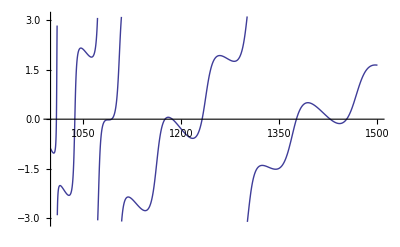

```mathematica
Plot[Arg[DD], {EE, 1000.0, 1500.0}]
```

```mathematica
Plot3D[Norm[psi[x]]^2,{x,0.0,5.0},{EE, 1000,1500.0}]
```

-Graphics3D-